```mathematica
1-(n^2.5+n)/(n+1)^2.5
```

1-(n+n^2.5)/(1+n)^2.5

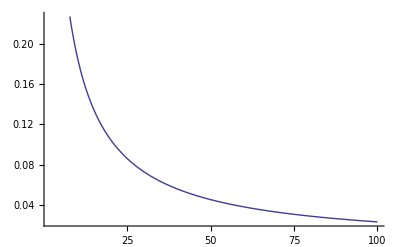

```mathematica
Plot[%,{n,2,100}]
```

```mathematica
7!
```

5040

```mathematica
0-(-0.83333333333333337`50*(-2000000000.0000000`50))
```

-1.66666666666666674×10^9

```mathematica
(-5.8207660913467422`50*10^(-16))(1.4551915228366858`50*10^(-11))
```

```mathematica
-8.47032947254300914551095047500076`49.69897000433602*^-27
-8.4703294725430098e-027
```

```mathematica
-1.4551915228366858`50*4.3655745685100566`50
```

-6.35274710440725678637363671441628

```mathematica
-6.3527471044072570e-027
```

```mathematica
1.4551915228366858`50*4.3655745685100566`50
```

6.35274710440725678637363671441628

```mathematica
6.3527471044072570e-027
```

```mathematica
100000.00000000012`50+8.4703294725430098`50*10^(-27)
```

100000.0000000001200000000000000084703294725430098

```mathematica
99999.999999999913`50-8.4703294725430098`50*10^(-27)
```

99999.9999999999129999999999999915296705274569902

```mathematica
M=10^5*{{-1,-1,-1,0,1},{-1,-1,0,-1,0},{-1,0,-1,-1,0},{0,-1,-1,-1,0},{0,0,0,-1,0}}
```

{{-100000,-100000,-100000,0,100000},{-100000,-100000,0,-100000,0},{-100000,0,-100000,-100000,0},{0,-100000,-100000,-100000,0},{0,0,0,-100000,0}}

```mathematica
Det[M]
```

-20000000000000000000000000

```mathematica
M={{-1,-1,-1,-1,-1,0,0,1,1},{-1,-1,-1,0,-1,-1,0,0,0},{-1,0,0,0,0,0,1,1,0},{0,-1,0,0,-1,0,1,1,1},{0,-1,0,0,0,0,0,1,1},{0,-1,0,0,0,0,1,1,0},{0,0,-1,0,-1,0,1,1,1},{0,0,0,0,-1,0,0,1,1},{0,0,0,0,-1,0,1,0,1}}
```

{{-1,-1,-1,-1,-1,0,0,1,1},{-1,-1,-1,0,-1,-1,0,0,0},{-1,0,0,0,0,0,1,1,0},{0,-1,0,0,-1,0,1,1,1},{0,-1,0,0,0,0,0,1,1},{0,-1,0,0,0,0,1,1,0},{0,0,-1,0,-1,0,1,1,1},{0,0,0,0,-1,0,0,1,1},{0,0,0,0,-1,0,1,0,1}}

```mathematica
MatrixForm[M]
```

(-100000 | -100000 | -100000 | -100000 | -100000 | 0 | 0 | 100000 | 100000
-100000 | -100000 | -100000 | 0 | -100000 | -100000 | 0 | 0 | 0
-100000 | 0 | 0 | 0 | 0 | 0 | 100000 | 100000 | 0
0 | -100000 | 0 | 0 | -100000 | 0 | 100000 | 100000 | 100000
0 | -100000 | 0 | 0 | 0 | 0 | 0 | 100000 | 100000
0 | -100000 | 0 | 0 | 0 | 0 | 100000 | 100000 | 0
0 | 0 | -100000 | 0 | -100000 | 0 | 100000 | 100000 | 100000
0 | 0 | 0 | 0 | -100000 | 0 | 0 | 100000 | 100000
0 | 0 | 0 | 0 | -100000 | 0 | 100000 | 0 | 100000)

```mathematica
Det[M]//N
```

1.

```mathematica
Log[1.1]/Log[10]
```

0.0413927

```mathematica
Log[10.0]
```

2.30259

```mathematica
Exp[0.69314]
```

1.99999

```mathematica
Log[2]/Log[1.1]
```

7.27254

```mathematica
f[x_]:=-2.51983856413184845799999999999999999998`18.190605497678977+1.87027485120495290911428571428571428571`18.190605497678977 x+0.18964443086097114228571428571428571429`18.190605497678977 x^2;
```

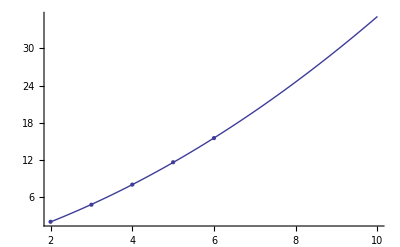

```mathematica
Show[ListPlot[{{2,2},{3,4.754887502163468227},{4,8},{5,11.609640474436812241},{6,15.50977500432693823}}],Plot[f[x],{x,2,10}]]
```

```mathematica
lm=LinearModelFit[{{2,2},{3,4.754887502163468227},{4,8},{5,11.609640474436812241},{6,15.50977500432693823}},{x,x^2},x]
```

```mathematica
f[7]
```

```mathematica
Normal[Series[f[x],{x,5,3}]]/.x->x+1
```

```mathematica
g[x_]:=11.57264646341719464471428571428571428583`18.033607801451257+3.76671915981466433197142857142857142861`18.190605497678977 (-4+x)+0.18964443086097114228571428571428571429`18.190605497678977 (-4+x)^2
```

```mathematica
g[0]
```

-0.4599192820659244

```mathematica
M={{-1,-1,-1,-1,-1,0,0,1,1},
{-1,-1,-1,0,-1,-1,0,0,0},
{-1,0,0,0,0,0,1,1,0},
{2,-1,1,1,-1,0,1,0,1},
{-1,-2,0,1,2,-1,-1,2,1},
{2,-2,-1,-2,-1,1,2,0,-2},
{3,2,-3,3,1,-1,0,1,2},
{1,1,0,2,-2,-2,-2,4,0},
{2,-1,2,-3,2,-5,1,0,1}};
```

```mathematica
Det[M]
```

57600

```mathematica
MatrixForm[M]
```

(-1 | -1 | -1 | -1 | -1 | 0 | 0 | 1 | 1
-1 | -1 | -1 | 0 | -1 | -1 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
2 | -1 | 1 | 1 | -1 | 0 | 1 | 0 | 1
-1 | -2 | 0 | 1 | 2 | -1 | -1 | 2 | 1
2 | -2 | -1 | -2 | -1 | 1 | 2 | 0 | -2
3 | 2 | -3 | 3 | 1 | -1 | 0 | 1 | 2
1 | 1 | 0 | 2 | -2 | -2 | -2 | 4 | 0
2 | -1 | 2 | -3 | 2 | -5 | 1 | 0 | 1)

```mathematica
A=M
```

{{-1,-1,-1,-1,-1,0,0,1,1},{-1,-1,-1,0,-1,-1,0,0,0},{-1,0,0,0,0,0,1,1,0},{2,-1,1,1,-1,0,1,0,1},{-1,-2,0,1,2,-1,-1,2,1},{2,-2,-1,-2,-1,1,2,0,-2},{3,2,-3,3,1,-1,0,1,2},{1,1,0,2,-2,-2,-2,4,0},{2,-1,2,-3,2,-5,1,0,1}}

```mathematica
A=M;denom=1;sign=1;k=0;
```

```mathematica
k++;For[i=k,(i<n)&&A[[i+1,k+1]]==0,i++];i
```

1

```mathematica
If[i==n,det=0;Break;]
```

```mathematica
For[j=k,j<n,j++,det=A[[k+1,j+1]];A[[k+1,j+1]]=A[[i+1,j+1]];A[[i+1,j+1]]=det];sign=-sign;
```

```mathematica
pivot=A[[k+1,k+1]]
```

-1

```mathematica
For[i=k+1,i<n,i++,
temp=A[[i+1,k+1]];
For[j=k+1,j<n,j++,A[[i+1,j+1]]=(A[[i+1,j+1]]*pivot-temp*A[[k+1,j+1]])/denom;]]
denom=pivot;
```

```mathematica
Diagonal[A]
MatrixForm[A]
```

{-1,-1,0,-1,-4,-3,0,-4,-1}

(-1 | -1 | -1 | -1 | -1 | 0 | 0 | 1 | 1
-1 | -1 | -1 | 0 | -1 | -1 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0
2 | -1 | -2 | -1 | 0 | -1 | -1 | 0 | -1
-1 | -2 | -2 | -1 | -4 | -1 | 1 | -2 | -1
2 | -2 | -1 | 2 | -1 | -3 | -2 | 0 | 2
3 | 2 | 5 | -3 | 1 | 3 | 0 | -1 | -2
1 | 1 | 1 | -2 | 3 | 3 | 2 | -4 | 0
2 | -1 | -3 | 3 | -3 | 4 | -1 | 0 | -1)

```mathematica
denom*sign
```

57600

```mathematica
k
```

8

```mathematica
sign
```

-1

```mathematica
Det[A]
```

57600

```mathematica
k
```

7